## Periodic chain

```mathematica
(* Tight-binding Hamiltonian for a tranlational invariant chain, with periodic bc *)
h[n_,V_]:=Block[{tbl,ar,mid=IntegerPart[n/2]},
(* jump amplitudes *)
tbl=Table[{i,i+1}->1.,{i,1,n-1}];
(* periodic bc *)
AppendTo[tbl,{1,n}->-1.];
(* scalar impurity at the middle of the chain *)
AppendTo[tbl,{mid,mid}->V/2];
ar=SparseArray[tbl,{n,n}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* wavefunctions and energies *)
n=500;
v=.1;
{en,eigs}=Eigensystem[h[n,v]];
ord=Ordering[en];
(* order eigenfunctions by increasing energy *)
eigs=eigs[[ord]];
en=en[[ord]];

v=0.;
{enRef,eigsRef}=Eigensystem[h[n,v]];
ordRef=Ordering[enRef];
eigsRef=eigsRef[[ordRef]];
enRef=enRef[[ordRef]];
```

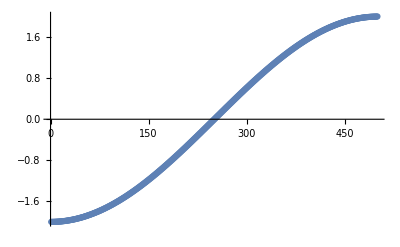

```mathematica
ListPlot[en]
```

### Local density of states (physically meaningless)

```mathematica
(* approximate Dirac delta *)
δ[x_,ϵ_]:=(ϵ/Pi)/(x^2+ϵ^2);
(*δ[x_,ϵ_]:=Max[1-Abs[x/ϵ],0]/ϵ;*)
```

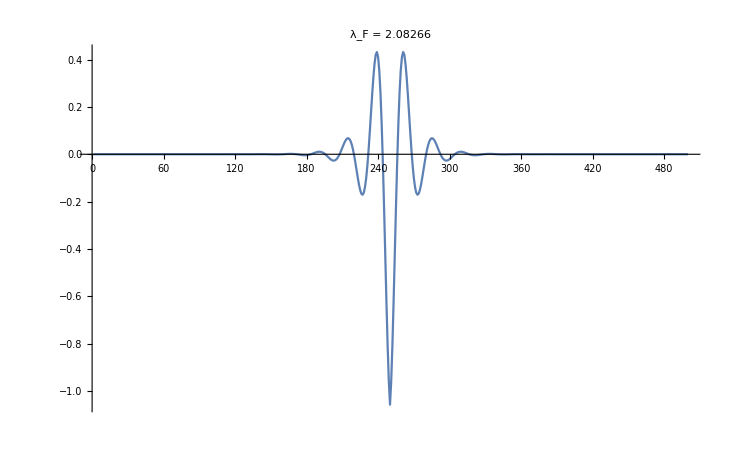

```mathematica
(* local density of states ρ(ω) for ω ∈ Spectrum *)
(*Clear[pos];
pos[i_]:=(2Pi/√(2Abs[enRef[[i]]]))^-1 Range[n];*)
ω=en[[20]];
(* index wavefunctions by energies, take their square *)
int=Transpose[eigs]^2;
intRef=Transpose[eigsRef]^2;
ϵ=0.01;
deltalist=δ[ω-#,ϵ]&/@en;
deltalistRef=δ[ω-#,ϵ]&/@enRef;
(* local density of states: Subscript[ρ, ii](ω) = Subscript[Σ, a] int(i,a)^2 Subscript[δ, ϵ](ω-Subscript[E, a]) *)
rho=int.deltalist;
(* local density in absence of impurity *)
rhoRef=intRef.deltalistRef;
(* change in density when we add the impurity *)
drho=rho-rhoRef;
λf=(2Pi)/ArcCos[ω/2];
ListPlot[drho,PlotRange->All,Joined->True,PlotLabel->"λ_F = "<>ToString[λf]]
(*Plot[(λf/2) drho[[IntegerPart[n/2]]]Sin[2 (x-n/2)/λf]/(x-n/2),{x,0,n},Epilog->Point@MapThread[{#1,#2}&,{Range[n],drho}],PlotRange->All]*)
```

### Integrated local density of states

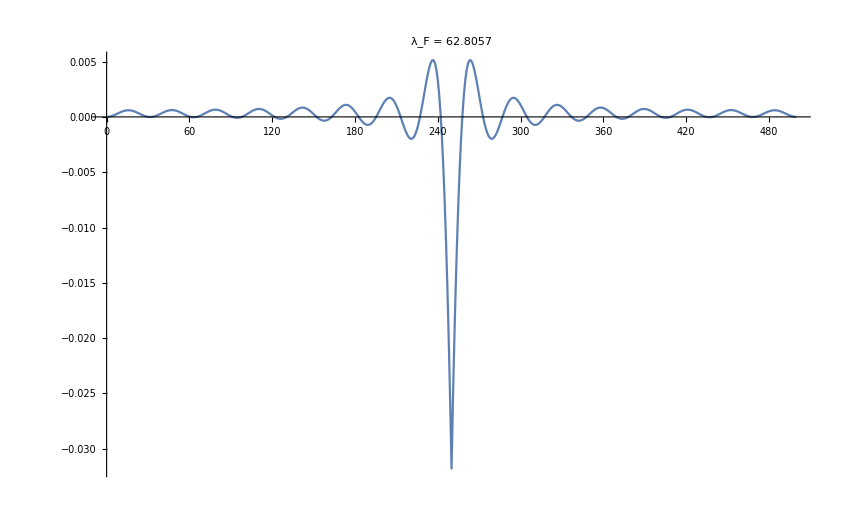

```mathematica
(* chemical potential *)
mu=1.99;
(* find the index of the lowest energy level larger than the chemical potential *)
FirstPosition[en,e_ /; e>mu]//First;
(* index of the highest energy level smaller than the chemical potential *)
If[%==Missing["NotFound"],am=n,,am=%-1];
(* index wavefunctions by energies, keep components up to the Fermi level, take their square *)
int=(eigs[[;;am]])^2;
intRef=(eigsRef[[;;am]])^2;
(* difference in integrated local density of states *)
dPhi=(Plus@@int)-(Plus@@intRef);
(* wavelength at the Fermi level *)
λf=(2Pi)/ArcCos[mu/2];
ListPlot[dPhi,PlotRange->All,Joined->True,PlotLabel->"λ_F = "<>ToString[λf]]
```

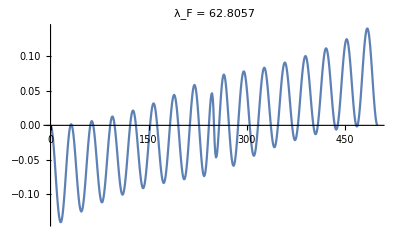

```mathematica
(* relative distance to the impurity *)
relx=Table[i-IntegerPart[n/2],{i,1,n}];
(* integrated densiy of states times the relative distance *)
dPhix=relx*dPhi;
ListPlot[dPhix,PlotRange->All,Joined->True,PlotLabel->"λ_F = "<>ToString[λf]]
```

## Fibonacci in the direct basis

```mathematica
τ=N [(1+Sqrt[5])/2];
rot=28;
fib[n_]:=IntegerPart[τ^-1( n+1+rot)]-IntegerPart[τ^-1 (n+rot)];
jump[n_,tw_]:=If[fib[n-1]<1,1.,tw];
```

```mathematica
Clear[hf];
hf[n_,tw_,V_]:=Block[{F2=Fibonacci[n+2],tbl,ar,mid},
(* middle site *)
mid = IntegerPart[F2/2];
(* jump amplitudes *)
tbl=Table[{i,i+1}->jump[i,tw],{i,1,F2-1}];
(* periodic boundary conditions *)
AppendTo[tbl,{1,F2}->tw];
(* scalar impurity at the middle of the chain *)
AppendTo[tbl,{mid,mid}->V/2];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

### Oscillations in direct space in the weak quasiperiodicity limit

```mathematica
(* wavefunctions and energies *)
n=10;
(* weak qp: Subscript[t, w] -> 1 *)
tw=.9;
v=1.;
{en,eigs}=Eigensystem[hf[n,tw,v]];
ord=Ordering[en];
(* order eigenfunctions by increasing energy *)
eigs=eigs[[ord]];
en=en[[ord]];

v=0.;
{enRef,eigsRef}=Eigensystem[hf[n,tw,v]];
ordRef=Ordering[enRef];
eigsRef=eigsRef[[ordRef]];
enRef=enRef[[ordRef]];
```

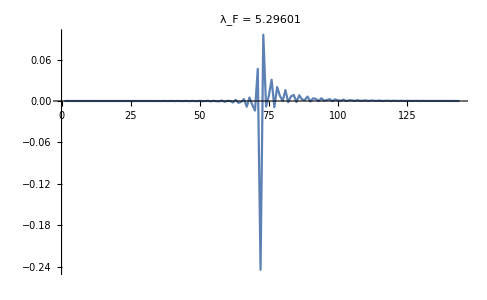

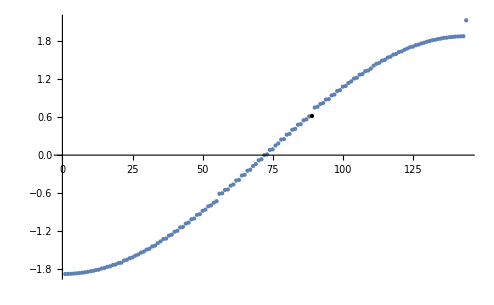

```mathematica
(* chemical potential *)
mu=0.75;
(* find the index of the lowest energy level larger than the chemical potential *)
FirstPosition[en,e_ /; e>mu]//First;
(* index of the highest energy level smaller than the chemical potential *)
If[%==Missing["NotFound"],am=n,,am=%-1];
(* index wavefunctions by energies, keep components up to the Fermi level, take their square *)
int=(eigs[[;;am]])^2;
intRef=(eigsRef[[;;am]])^2;
(* difference in integrated local density of states *)
dPhi=(Plus@@int)-(Plus@@intRef);
(* wavelength at the Fermi level *)
λf=(2Pi)/ArcCos[mu/2];
ListPlot[dPhi,PlotRange->All,Joined->True,PlotLabel->"λ_F = "<>ToString[λf]]

ListPlot[en,Epilog->{PointSize[Medium],Point[{am,en[[am]]}]},PlotStyle->PointSize[Medium]]
```